```mathematica
pic[n_,f_]:=(2f Sin[f Log[n]]+Cos[f Log[n]])Sum[j^(-1/2)Sin[f Log[j]],{j,1,n}]+(2f Cos[f Log[n]]-Sin[f Log[n]])Sum[j^(-1/2)Cos[f Log[j]],{j,1,n}]
```

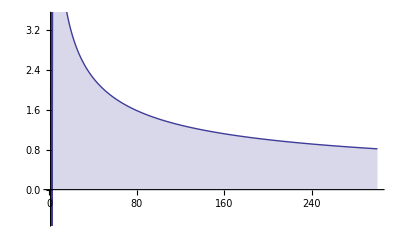

```mathematica
DiscretePlot[pic[n,Im[ZetaZero[1]]],{n,1,300}]
```